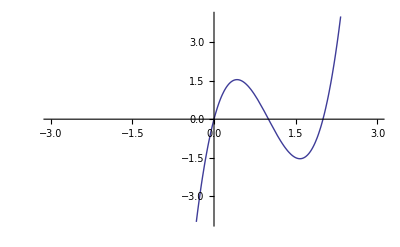

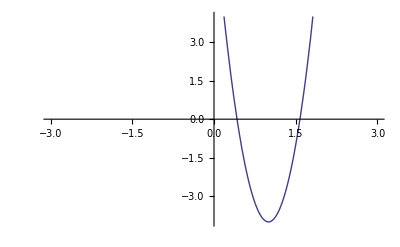

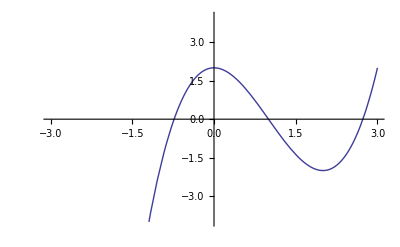

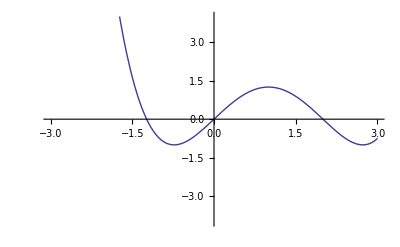

```mathematica
cubic1=Plot[4*x^3-12*x^2+8*x,{x,-3,3},PlotRange->{-4,4}]
quad=Plot[12*x^2-24*x+8,{x,-3,3},PlotRange->{-4,4}]
cubic2=Plot[x^3-3*x^2+2,{x,-3,3},PlotRange->{-4,4}]
quart=Plot[x^4/4-x^3+2x,{x,-3,3},PlotRange->{-4,4}]
```

```mathematica
Export["cubic1.png",cubic1]
Export["cubic2.png",cubic2]
Export["quad.png",quad]
Export["quart.png",quart]
```

cubic1.png

cubic2.png

quad.png

quart.png

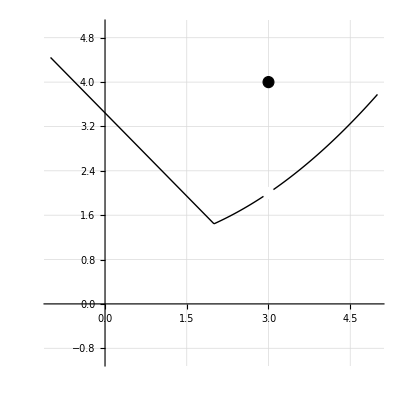

```mathematica
curve1=Plot[(x/3)^2+1, {x,2,5},PlotStyle->{Black,Thick},PlotRange->{{-1,5},{-1,5}},GridLines->Automatic,AspectRatio->1];
curve2=Plot[-x+3.4444, {x,-1,2},PlotStyle->{Black,Thick},PlotRange->{{-1,5},{-1,5}},GridLines->Automatic,AspectRatio->1];
circ=Graphics[{{EdgeForm[Thick],White,Disk[{3,2},.1]},{EdgeForm[Thick],Black,Disk[{3,4},.1]}}];
isDiff=Show[curve1,curve2,circ]
```

```mathematica
Export["isDiff.png",isDiff]
```

isDiff.png